```mathematica
(* Radiative Quenching, Chapter 3 *)
(* This one uses my paper *)

(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
μ=Subscript[m, p]/2;
hbar= 1;  
hbarSI =1.054571817*^-34;
cLight=137.036 ;(*SpeedOfLight, atomic units*)
cLightSI= 299792458 ;(*SpeedOfLight, m/s*)
oneSec = 2.418884326509*^-17;  (* 1 sec SI <-> 1 sec AU *)
aBorh = 5.29177*^-11;   (* Si <-> AU *)

(* RawData format R,E, E + 1/R,A,p *)

vSg1RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx"];
vSu2RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx"];


vSg1Data =vSg1RawData[[1;;44]];
vSu2Data = vSu2RawData[[1;;44]];

vSu2Data[[9]]
```

{1.,-2.01521,-1.01521,7.84906,1.0038}

```mathematica
(* Calculate the Transition Dipole Moment *)
(* Upper Limit for integration *)
maxR = vSg1Data[[Length[vSg1Data]]][[1]];
Print["maxR=",maxR]
maxR = 20;
maxIndex = 30;

Print["R=",vSg1Data[[maxIndex,1]], ", A=",vSg1Data[[maxIndex,4]],", p=", vSg1Data[[maxIndex,5]]];
Print["R=",vSu2Data[[maxIndex,1]], ", A=",vSu2Data[[maxIndex,4]],", p=", vSu2Data[[maxIndex,5]]];
```

maxR=31

R=17, A=157862., p=17.2473

R=17, A=27187., p=17.248

0.00074606

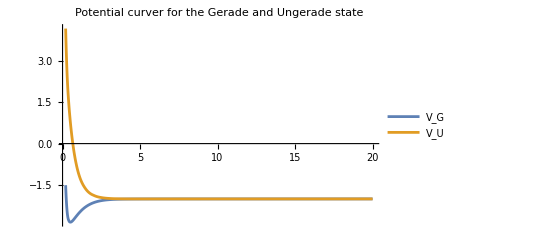

```mathematica
(* Load Potential curves for 1sg, 2sg states 
"R,E, E + 1/R,A,p *)
(* 1sg state, potential curve *)
vG=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,3]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
vU=Interpolation[Transpose[{vSu2Data[[All,1]],vSu2Data[[All,3]]}], InterpolationOrder->3];

deltaV[r_]:=Abs[vG[r]-vU[r]];
deltaV[20]
Plot[{vG[r],vU[r]},{r,0.2,maxR}, PlotRange->Full, PlotLegends->{"V_G","V_U"}, PlotLabel->"Potential curver for the Gerade and Ungerade state"]
```

```mathematica
(* Compute the Dipole momement D(r) for the single value of R *)
singleDR[R_,a1_,p1_,a2_,p2_, maxDistance_]:=Module[{norm1, norm2,dInt, l1,l2,m1,m1a,m2,m2a,lmNorm1, lmNorm2},
(* 1s wavefunction *)
l1=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a1 +2 R ξ -p1^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1 },L,{ξ,1.001,maxDistance}];
m1a=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] + (-a1 + p1^2 η^2)M[η]==0, M'[0]==0,M[.999]==1}, M,{η,0,.999}];
(* 2s wavefunction *) 
l2=NDSolveValue[{(ξ^2-1)L''[ξ]+ξ * L'[ξ]+ (a2+2 R ξ -p2^2 ξ^2)L[ξ]==0 ,L[1.001]==0,L'[1.001]==1},L,{ξ,1.001,maxDistance}];
m2a=NDSolveValue[{(1-η^2)M''[η]-η *M'[η] + (-a2 + p2^2 η^2)M[η]==0, M'[0]==0,M[0.999]==1}, M,{η,0,.999}];

m1[x_]:=If[x>=0,m1a[x],m1a[-x]];
m2[x_]:=If[x>=0,m2a[x],m2a[-x]];

Print["R=",R];
(* Compute <ψ|ψ> = <Subscript[ψ, 1s]|Subscript[ψ, 1s]> + <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
(* <Subscript[ψ, 1s]|Subscript[ψ, 1s]> *)
norm1=Sqrt[NIntegrate[Abs[l1[ξ] m1[η]]^2,{η,-.999,.999},{ξ,1.001,maxDistance}]];
(* <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
norm2=Sqrt[NIntegrate[Abs[l2[ξ]m2[η]]^2,{η,-.999,.999},{ξ,1.001,maxDistance}]];

lmNorm1[ξ_,η_]:=1/norm1 l1[ξ]m1[η];
lmNorm2[ξ_,η_]:=1/norm2 l2[ξ]m2[η];

dInt=(R/2)^3 NIntegrate[Conjugate[lmNorm1[ξ,η]]ξ η lmNorm2[ξ,η]((ξ^2-η^2)/(√(ξ^2-1)√(1-η^2))),{η,-0.999,0.999},{ξ,1.001,maxDistance}];
{R,dInt }
];

(*singleDR[vSg1Data[[24]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],5]
singleDR[vSg1Data[[14]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],5]
singleDR[vSg1Data[[15]][[1]],vSg1Data[[20]][[4]],vSg1Data[[20]][[5]],vSu2Data[[20]][[4]],vSu2Data[[20]][[5]],5]*)
```

```mathematica
(* Get all Rs, and coefficients A and p and calculate D(R) for all Rs *)
(* RawData format R,E, E + 1/R,A,p *)
inputData = Transpose[{vSg1Data[[1;;maxIndex,1]],vSg1Data[[1;;maxIndex,4]],vSg1Data[[1;;maxIndex,5]],vSu2Data[[1;;maxIndex,4]],vSu2Data[[1;;maxIndex,5]]}];

allDR =Map[singleDR[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]], maxR] &, inputData];
```

R=0.2

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.17101×10^-13 and 6.00846×10^-8 for the integral and error estimates.

R=0.3

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.99866×10^-12 and 9.64969×10^-8 for the integral and error estimates.

R=0.4

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.30211×10^-15 and 5.76465×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

R=0.5

R=0.6

R=0.7

R=0.8

R=0.9

NDSolveValue::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

R=1.

NDSolveValue::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

R=1.1

R=1.5

NDSolveValue::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

General::stop: Further output of NDSolveValue::bvluc will be suppressed during this calculation.

R=2.

R=2.5

```mathematica
allDR // MatrixForm
```

```mathematica
(* Dipole moment in SI units *)
drAUtoSI = 8.478*^-30; (* Cm *)
allDRSI=allDR;
allDRSI[[All,2]] =allDR[[All,2]]*drAUtoSI;
allDRSI

dR =Interpolation[Transpose[{allDR[[All,1]],allDR[[All,2]]}], InterpolationOrder->3];
Plot[dR[r],{r,0.1, 7}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R)(in a.u.)"}, PlotRange->Full]

dRSI =Interpolation[Transpose[{allDRSI[[All,1]],allDRSI[[All,2]]}], InterpolationOrder->3];
Plot[dRSI[r],{r,0.1, maxR}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R) (units of C m)"}, PlotRange->Full, Axes->True]
```

```mathematica
aR[R_]:=4/(3hbar cLight^3)(dR[R])^2((vU[R]-vG[R])/hbar)^3;

aRAUtoSI = 4.1341*^16;
aRSI[R_]:=aR[R]*aRAUtoSI;

aRSI2[R_]:=4/(3 hbarSI cLightSI^3)(dRSI[R])^2(((vU[R]-vG[R])4.35974*^-18)/hbarSI)^3;


Plot[aR[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R)"}, PlotRange->Full]
Plot[aRSI[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R) (s^-1)"}, PlotRange->Full]
Plot[aRSI2[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A2(R) (s^-1)"}, PlotRange->Full]
```

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-